## Лабораторная работа №5 Radionchik S.S.

## Задание 1.

Объяснить результаты.

Пробел выполняет роль знака умножения

```mathematica
3*5
3 5
```

15

15

Введение дополнительных пробелов не изменяют результата вычислений

```mathematica
3                5
```

15

```mathematica
2+        7
```

9

При обработке производятся лишь возможные упрощения, но сами числа остаются точными и преобразуются в числа, заданные приближенно, только по команде пользователя.

```mathematica
2/3
```

2/3

```mathematica
17^(1/2)
```

√17

Действительные числа, содержащие десятичную точку, считаются заданными приближенно. Поэтому выражения, в которые входят действительные числа, вычисляются приближенно без специальной команды.

```mathematica
3     /7.
```

0.428571

```mathematica
17.      ^(1/2)
```

4.12311

## Задание 2

С помощью функции N вычислить 17^(1/2) с точностью до 200 значащих цифр. Провериться потом с помощью Precision

```mathematica
result=N[Sqrt[17], 200] (*численное приближение до 200 значащий цифр*)
```

4.1231056256176605498214098559740770251471992253736204343986335730949543463376215935878636508106842966845440409392141416153014208404158683630795481457469069776770232664362408630877905675723857082255214

```mathematica
Precision[result]
```

200.

Найти приближенное значение числа E^(Pi *Sqrt[163]) с точностью до 40 значащих цифр. Вычислить насколько полученный результат отличается от ближайшего к нему целого числа. Для стандартного округления используйте функцию Round[x].

```mathematica
result=N[E^(Pi *Sqrt[163]), 40]
Round[result]
```

2.625374126407687439999999999992500725972×10^17

262537412640768744

Вычислить

```mathematica
(10*((10.8*10^3)/300)^(1/2) + 4)^(1/3)
```

4.

```mathematica
(10^-24 10^12)/10^-14 √(32768/2^9)
```

800

Последовательно введите выражение

```mathematica
5>3
5<2
```

True

False

Справедливо ли неравенство. Найти численные значения и убедиться в правильности.

```mathematica
Pi^E>E^Pi
```

False

```mathematica
N[Pi^E, 10]
N[E^Pi, 10]
```

22.45915772

23.14069263

## Задание 3

Решить уравнения

```mathematica
NSolve[√(x+2)+4  x == 4, x]
```

{{x→0.597111}}

```mathematica
NSolve[x^3-3  x^2+5 == 0, x] (*комплексные*)
```

{{x→-1.1038},{x→2.0519-0.565236 ⅈ},{x→2.0519+0.565236 ⅈ}}

Решить системы уравнений

```mathematica
NSolve[{x^2+x y+y^2==1, x^3+x^2 y+x y^2+y^3==4}, {x,y}]
```

{{x→-1.-1.41421 ⅈ,y→-1.+1.41421 ⅈ},{x→-1.+1.41421 ⅈ,y→-1.-1.41421 ⅈ},{x→1.6838+0.133552 ⅈ,y→-0.683802-1.13355 ⅈ},{x→1.6838-0.133552 ⅈ,y→-0.683802+1.13355 ⅈ},{x→-0.683802-1.13355 ⅈ,y→1.6838+0.133552 ⅈ},{x→-0.683802+1.13355 ⅈ,y→1.6838-0.133552 ⅈ}}

```mathematica
NSolve[{x-y^2+3z == 34, x+y-z==-1, -x+2y+3z ==4}, {x,y,z}]
```

{{x→9.25-10.2317 ⅈ,y→-3.5+4.09268 ⅈ,z→6.75-6.13901 ⅈ},{x→9.25+10.2317 ⅈ,y→-3.5-4.09268 ⅈ,z→6.75+6.13901 ⅈ}}

Придумать свою

```mathematica
NSolve[{58x-14y==-15, x^2 y+y^2+x^5+ 58== 115}, {x,y}, Reals]
Length [%]
```

{{x→1.30739,y→6.48776}}

1

## Задание 4 Вариант 17

Используя функцию FindRoot решить уравнение

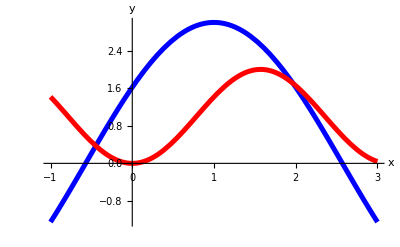

```mathematica
Plot[{3 *Cos[x -1], 2*(Sin[x])^2}, {x,-1,3}, PlotStyle->{{Thickness[0.009], RGBColor[0,0,1]}, {Thickness[0.009], RGBColor[1,0,0]}}, AxesLabel->{"x", "y"}]
```

```mathematica
FindRoot[3 *Cos[x -1] == 2*(Sin[x])^2, {x,-0.5}]
FindRoot[3 *Cos[x -1] == 2*(Sin[x])^2, {x,2}]
```

{x→-0.446281}

{x→1.96813}

## Задание 5 Вариант 17

Найти решение диф.уравнения на заданном отрезке.
1) найти корни уравнения y(x) = 0
2) найти значение производной y’(x) в точках, где y(x) = 0
3) выбрать одну из точек, где производная равна нулю и найти значение функции в этой точке
4) с помощью FindMinimum найти точки, в которых функция y(x) имеет локальный минимум или максимум. сравнить результаты с предыдущим пунктом.

```mathematica
dSol=NDSolve[{y''[x]-y'[x]+ 2y [x](Cos[x])^2==0, y[0]==1, y'[0]==-2},y, {x,-1,5}]
```

{{y→InterpolatingFunction[…]}}

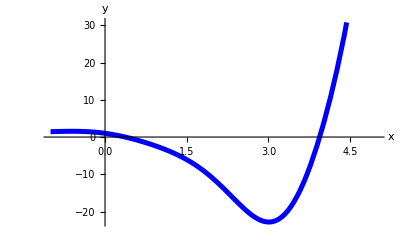

```mathematica
Plot[y[x]/.dSol, {x,-1,5}, AxesLabel->{"x", "y"}, PlotStyle->{RGBColor[0,0,1], Thickness[0.009]}]
```

```mathematica
solRoot1=FindRoot[(y[x]/.dSol[[1]])==0, {x,4}] 
solRoot2 = FindRoot[(y[x]/.dSol[[1]])==0, {x,0.3}] 
(*корень уравнения*)
```

{x→3.93939}

{x→0.368342}

```mathematica
D[y[x]/.dSol[[1]],x]/.solRoot1 
D[y[x]/.dSol[[1]],x]/.solRoot2 
(*значение производной в найденной точке*)
```

48.7465

-3.39049

```mathematica
sol2=FindRoot[D[y[x]/.dSol[[1]],x]==0, {x,3}] (*локальный минимум*)
```

{x→3.00679}

```mathematica
y[x]/.dSol[[1]]/.sol2 (*соответствующее значение функции*)
```

-22.8036

```mathematica
FindMinimum[y[x]/.dSol[[1]], {x,3}] (*минимальное значение функции*)
(*полученные значения совпадают*)
```

{-22.8036,{x→3.00679}}

## Задание 6 2

Используя ф-цию Table определите список численных данных элементов (x, y). Выберите шаг и область изменения x. С помощью Random внесите в каждой точке x случайное возмущение.
1) изобразите полученные точки на координатной плоскости.
2) Используя Fit найдите наилучшую кривую, аппроксимирующую численные данные
3) Изобразите найденную кривую вместе с экспериментальными точками

```mathematica
result = Table[{x,(4+2x+115Sin[x]+12Cos[x])(1+Random[Real, {-0.1, 0.1}])}, {x,0,9,0.25}]
```

{{0.,14.8797},{0.25,42.3393},{0.5,74.5176},{0.75,89.519},{1.,108.673},{1.25,127.654},{1.5,115.137},{1.75,119.464},{2.,112.38},{2.25,87.7407},{2.5,63.8467},{2.75,43.4549},{3.,15.2881},{3.25,-13.1778},{3.5,-41.313},{3.75,-60.6558},{4.,-88.027},{4.25,-98.3109},{4.5,-100.396},{4.75,-107.649},{5.,-98.1286},{5.25,-78.5157},{5.5,-56.6684},{5.75,-29.3834},{6.,-4.73345},{6.25,23.5706},{6.5,54.9943},{6.75,82.7564},{7.,95.6153},{7.25,118.308},{7.5,129.629},{7.75,125.241},{8.,130.348},{8.25,111.725},{8.5,100.669},{8.75,83.9348},{9.,59.7343}}

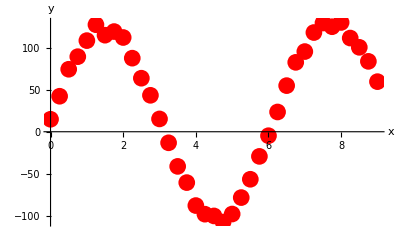

```mathematica
resultPlot=ListPlot[result, PlotStyle->{ Red,PointSize[0.03]}, AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[result, {1,x,Sin[x], Cos[x]},x]
```

4.59903+1.61383 x+12.2609 Cos[x]+114.579 Sin[x]

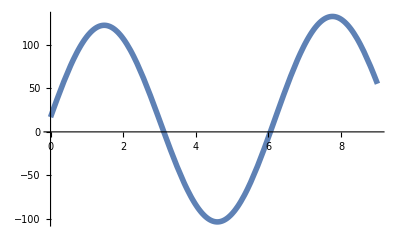

```mathematica
plot2 =Plot[{y1}, {x,0,9},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

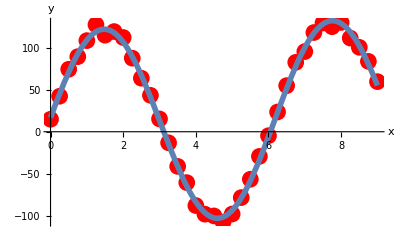

```mathematica
Show[resultPlot, plot2]
```

## Задание 6 1

```mathematica
result = Table[{x,(4+2x+15x^2+12x^3 + 7x^4)(1+Random[Real, {-0.1, 0.1}])}, {x,0,9,0.25}]
```

{{0.,4.32987},{0.25,6.01339},{0.5,11.4431},{0.75,20.2946},{1.,40.4767},{1.25,74.93},{1.5,108.74},{1.75,190.063},{2.,289.819},{2.25,378.743},{2.5,574.505},{2.75,742.683},{3.,946.525},{3.25,1235.15},{3.5,1660.19},{3.75,2437.18},{4.,2789.78},{4.25,3421.78},{4.5,4531.94},{4.75,5070.84},{5.,6710.5},{5.25,7170.74},{5.5,9080.87},{5.75,10712.2},{6.,13305.3},{6.25,14135.},{6.5,17313.},{6.75,18336.3},{7.,21175.2},{7.25,25489.},{7.5,28666.},{7.75,32796.6},{8.,36756.4},{8.25,39624.8},{8.5,40599.1},{8.75,48819.7},{9.,56649.8}}

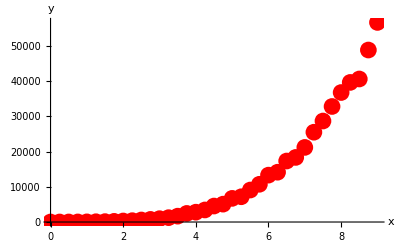

```mathematica
resultPlot=ListPlot[result, PlotStyle->{ Red,PointSize[0.03]}, AxesLabel->{"x", "y"}]
```

```mathematica
y1=Fit[result, {1,x,x^2,x^3, x^4},x]
```

43.7485-23.8305 x-32.1156 x^2+33.6195 x^3+5.0168 x^4

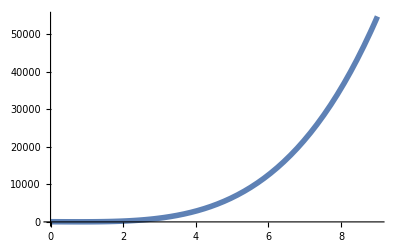

```mathematica
plot2 =Plot[{y1}, {x,0,9},PlotStyle->{{Thickness[0.01]},{Thickness[0.01],Dashing[{0.03}]}}]
```

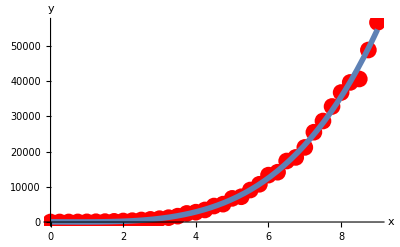

```mathematica
Show[resultPlot, plot2]
```